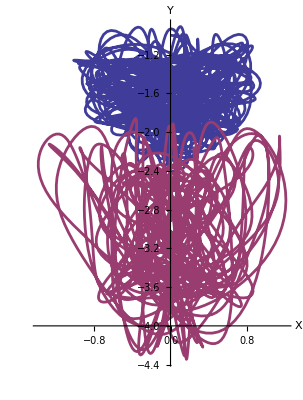

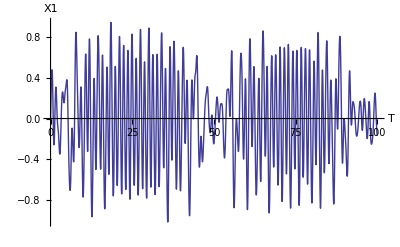

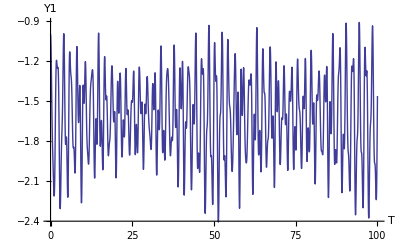

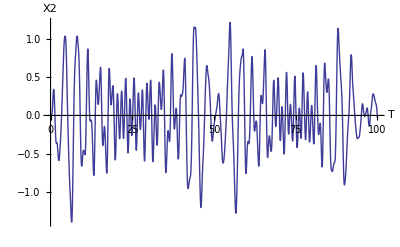

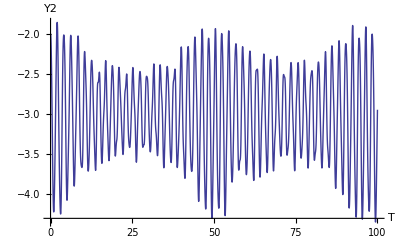

```mathematica
g=9.8;k1=3;k2=2;m1=0.1;m2=0.1;
L10=1;L20=1;tm=100;
initial1={0,1.4,-L10,0};
initial2={0,0.0,-(L10+L20),0};
L1[t]=√(x1[t]^2+y1[t]^2);
L2[t]=√((x2[t]-x1[t])^2+(y2[t]-y1[t])^2);
equs=
{m1*x1''[t]==
-k1*(L1[t]-L10)*x1[t]/L1[t]+k2*(L2[t]-L20)*(x2[t]-x1[t])/L2[t],
m1*y1''[t]==-m1*g+k1*(L1[t]-L10)*(-y1[t])/L1[t]-k2*(L2[t]-L20)*(y1[t]-y2[t])/L2[t],
m2*x2''[t]==-k2*(L2[t]-L20)*(x2[t]-x1[t])/L2[t],
m2*y2''[t]==-m2*g+k2*(L2[t]-L20)*(y1[t]-y2[t])/L2[t],
x1[0]==initial1[[1]],x1'[0]==initial1[[2]],
x2[0]==initial2[[1]],x2'[0]==initial2[[2]],
y1[0]==initial1[[3]],y1'[0]==initial1[[4]],
y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};
s=NDSolve[equs,{x1,x2,y1,y2},{t,0,tm}];
{x1,x2,y1,y2}={x1,x2,y1,y2}/.s[[1]];
ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}},{t,0,tm},
PlotRange->Automatic,
AxesLabel->{"X","Y"},AspectRatio->Automatic,
AxesStyle->Thickness[0.004],
PlotStyle->Thickness[0.005]]
Plot[x1[t],{t,0,100},AxesLabel->{"T","X1"}]
Plot[y1[t],{t,0,100},AxesLabel->{"T","Y1"}]
Plot[x2[t],{t,0,100},AxesLabel->{"T","X2"}]
Plot[y2[t],{t,0,100},AxesLabel->{"T","Y2"}]
Clear[g,equs,L10,L20,x1,y1,x2,y2,initial1,initial2]
```